# Approximation Figure

Ruvi Lecamwasam, ruvi.lecamwasam@anu.edu.au

### Fig 3a Comparing full simulation with approximation

#### Import Data

```mathematica
SetDirectory@NotebookDirectory[];

end=-1;
fullsyscsv=Import["fullsys.csv"];
t=fullsyscsv[[;;end,1]];
x=fullsyscsv[[;;end,2]];
px=fullsyscsv[[;;end,3]];
a2=fullsyscsv[[;;end,4]];
aϕ=fullsyscsv[[;;end,5]];
Print["Imported fullsys.csv"];

approxsyscsv=Import["approxsys.csv"];
xa=approxsyscsv[[;;end,2]];
pxa=approxsyscsv[[;;end,3]];
Print["Imported approxsys.csv"];

energycsv=Import["energy.csv"];
ℰ=energycsv[[;;end,2]];
dℰdτ=energycsv[[;;end,3]];
Print["Imported energy.csv"];

energyacsv=Import["energya.csv"];
ℰa=energyacsv[[;;end,2]];
dℰdτa=energyacsv[[;;end,3]];
Print["Imported energya.csv"];
```

Imported fullsys.csv

Imported approxsys.csv

Imported energy.csv

Imported energya.csv

#### Generate figures

```mathematica
labelStyle=Directive[FontSize->35,FontColor->Black,FontFamily->"Times New Roman"];
plotOpts=Sequence[PlotRange->All,ImageSize->Large,LabelStyle->labelStyle,AxesStyle->Thick,TicksStyle->Thick];
imgPaddingL={{70,All},{All,All}};
imgPaddingR={{80,All},{All,All}};
```

```mathematica
xPlot=ListLinePlot[{Transpose@{t,x},Transpose@{t,xa}},plotOpts,AxesLabel->{"τ̃","x̃"},ImagePadding->imgPaddingL];
pPlot=ListLinePlot[{Transpose@{t,px},Transpose@{t,pxa}},plotOpts,AxesLabel->{"τ̃","(p̃)_x"},ImagePadding->imgPaddingR];
ℰPlot=ListLinePlot[{Transpose@{t[[;;-2]],ℰ},Transpose@{t[[;;-2]],ℰa}},plotOpts,AxesLabel->{"τ̃","ℰ̃"},PlotLegends->Placed[{"Exact","Approximation"},{0.35,0.8}],ImagePadding->imgPaddingL];
dℰdτPlot=ListLinePlot[{Transpose@{t[[;;-2]],dℰdτ},Transpose@{t[[;;-2]],dℰdτa}},plotOpts,AxesLabel->{"τ̃","dℰ̃/dτ̃"},ImagePadding->imgPaddingR];
```

```mathematica
fullPlot=Grid[{{xPlot,pPlot},{ℰPlot,dℰdτPlot}}]
```

-Graphics-

```mathematica
SetDirectory@NotebookDirectory[];
Export["figEvaluatingApprox_Full.png",Rasterize[fullPlot,ImageResolution->300]];
```

### Fig 3b Comparison of heating rates

```mathematica
redMin = 10000;
redMax=12000;

tRed=t[[redMin;;redMax]];
dℰdτRed=dℰdτ[[redMin;;redMax]];
dℰdτReda=dℰdτa[[redMin;;redMax]];
```

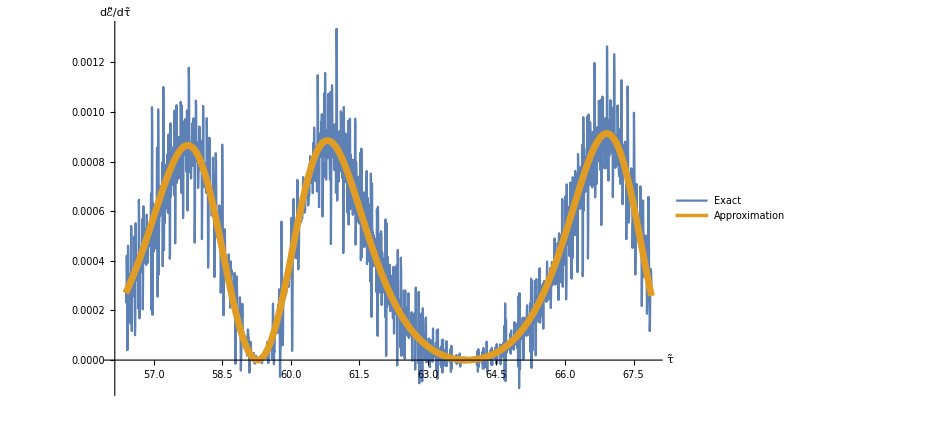

```mathematica
labelStyle=Directive[FontSize->30,FontColor->Black,FontFamily->"Times New Roman"];
plotOpts=Sequence[PlotRange->All,ImageSize->700,LabelStyle->labelStyle,AxesStyle->Thick,TicksStyle->Thick];
zoomedPlot=ListLinePlot[{Transpose@{tRed,dℰdτRed},Transpose@{tRed,dℰdτReda}},plotOpts,AxesLabel->{"τ̃","dℰ̃/dτ̃"},PlotLegends->Placed[{"Exact","Approximation"},Bottom],PlotStyle->{{},Thickness[0.007]}]
```

```mathematica
SetDirectory@NotebookDirectory[];
Export["figEvaluatingApprox_Zoomed.png",Rasterize[zoomedPlot,ImageResolution->300]];
```

### Fig 3c Trace at η=10

#### Import Data

```mathematica
SetDirectory@NotebookDirectory[];

end=-1;
fullsyscsv=Import["h10_fullsys.csv"];
t=fullsyscsv[[;;end,1]];
x=fullsyscsv[[;;end,2]];
px=fullsyscsv[[;;end,3]];
a2=fullsyscsv[[;;end,4]];
aϕ=fullsyscsv[[;;end,5]];
Print["Imported h10_fullsys.csv"];

approxsyscsv=Import["h10_approxsys.csv"];
xa=approxsyscsv[[;;end,2]];
pxa=approxsyscsv[[;;end,3]];
Print["Imported h10_approxsys.csv"];

energycsv=Import["h10_energy.csv"];
ℰ=energycsv[[;;end,2]];
dℰdτ=energycsv[[;;end,3]];
Print["Imported h10_energy.csv"];

energyacsv=Import["h10_energya.csv"];
ℰa=energyacsv[[;;end,2]];
dℰdτa=energyacsv[[;;end,3]];
Print["Imported h10_energya.csv"];
```

Imported h10_fullsys.csv

Imported h10_approxsys.csv

Imported h10_energy.csv

Imported h10_energya.csv

#### Generate figures

```mathematica
labelStyle=Directive[FontSize->35,FontColor->Black,FontFamily->"Times New Roman"];
plotOpts=Sequence[ImageSize->Large,LabelStyle->labelStyle,PlotStyle->Thick,AxesStyle->Thick,TicksStyle->Thick];
```

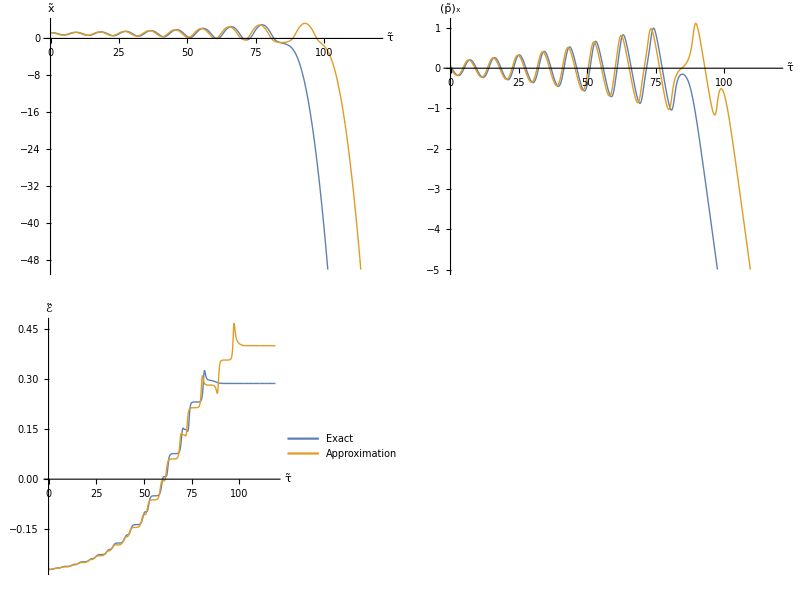

```mathematica
imgPaddingL={{60,All},{All,All}};
imgPaddingR={{80,All},{All,All}};
xPlot=ListLinePlot[{Transpose@{t,x},Transpose@{t,xa}},plotOpts,AxesLabel->{" τ̃","x̃"},PlotRange->{All,{-50,Automatic}},ImagePadding->imgPaddingL];
pPlot=ListLinePlot[{Transpose@{t,px},Transpose@{t,pxa}},plotOpts,AxesLabel->{" τ̃","(p̃)_x"},PlotRange->{All,{-5,All}},ImagePadding->imgPaddingR];
ℰPlot=ListLinePlot[{Transpose@{t[[;;-2]],ℰ},Transpose@{t[[;;-2]],ℰa}},plotOpts,AxesLabel->{" τ̃","ℰ̃"},PlotLegends->Placed[{"Exact","Approximation"},{0.35,0.8}],PlotRange->All,ImagePadding->imgPaddingL];
dℰdτPlot=ListLinePlot[{Transpose@{t[[;;-2]],dℰdτ},Transpose@{t[[;;-2]],dℰdτa}},plotOpts,AxesLabel->{" τ̃","dℰ̃/dτ̃"},PlotRange->All,ImagePadding->imgPaddingR];
fullPlot=Grid[{{xPlot,pPlot},{ℰPlot,dℰdτPlot}}]
```

```mathematica
SetDirectory@NotebookDirectory[];
Export["figEvaluatingApprox_h10.png",Rasterize[fullPlot,ImageResolution->300]];
```